```mathematica
f[a1_,x_,y_]=x-x*y/(1+a1*x)-0.01*x*x;
```

```mathematica
g[a1_,d0_,x_,y_]=-y+x*y/(1+a1*x)-d0*y*y;
```

```mathematica
funcr[a1_, d0_, x_] = -1-a1*x+x-d0*(1+2*a1*x+(a1^2)*x^2-0.01*x-0.02*a1*x^2-0.01*(a1^2)*x^3)
```

-1+x-a1 x-d0 (1-0.01 x+2 a1 x-0.02 a1 x^2+a1^2 x^2-0.01 a1^2 x^3)

```mathematica
Solve[{funcr[0.87,0.23,x]==0},x]
```

{{x→-0.810505-2.54101 ⅈ},{x→-0.810505+2.54101 ⅈ},{x→99.3222}}

```mathematica
equlibr[d0_]=Solve[{funcr[0.87,d0,x]==0},x];
```

```mathematica
Eq1X[d0_]=x//.equlibr[d0][[1]];
```

```mathematica
Eq2X[d0_]=x//.equlibr[d0][[2]];
```

```mathematica
Eq3X[d0_]=x//.equlibr[d0][[3]];
```

```mathematica
EqY[d0_,x_]= ((x/(1+0.87*x))-1)/d0
```

(-1+x/(1+0.87 x))/d0

```mathematica
Eq1X[0.23]
Eq2X[0.23]
Eq3X[0.23]
```

8.75029-1.77636×10^-14 ⅈ

4.68298+1.06581×10^-14 ⅈ

```mathematica
81.56673742427377+6.661338147750939*^-16 ⅈ
```

81.5667+6.66134×10^-16 ⅈ

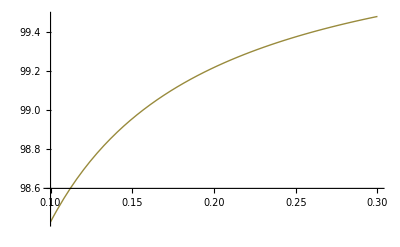

```mathematica
Plot[{Eq1X[d0],Eq2X[d0],Eq3X[d0]},{d0,0.1,0.3}]
```

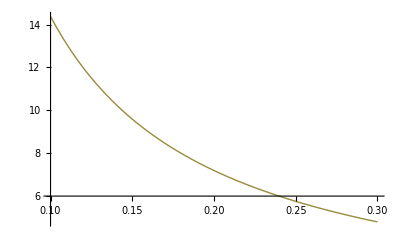

```mathematica
Plot[{EqY[d0,Eq1X[d0]], EqY[d0,Eq2X[d0]], EqY[d0,Eq3X[d0]]}, {d0, 0.1, 0.3}]
```

```mathematica
Export["C:\\1.eps",%]
```

Export::noopen: Cannot open "C:\\1.eps".

$Failed

```mathematica
fx[a1_,x_,y_]=D[f[a1,x,y],x];
```

```mathematica
fy[a1_,x_,y_]=D[f[a1,x,y],y];
```

```mathematica
gx[a1_,d0_,x_,y_]=D[g[a1,d0,x,y],x];
```

```mathematica
gy[a1_,d0_,x_,y_]=D[g[a1,d0,x,y],y];
```

```mathematica
det[a1_,d0_,x_,y_,lam_]=(fx[a1,x,y]-lam)*(gy[a1,d0,x,y]-lam)-fy[a1,x,y]*gx[a1,d0,x,y];
```

```mathematica
det1[d0_, x_, y_, lam_] = det[0.87,d0,x,y,lam];
```

```mathematica
re=Solve[{det1[d0, Eq1X[d0], EqY[d0, Eq1X[d0]], lam]==0},lam];
```

```mathematica
lam1[d0_] = lam/.re[[1]];
```

```mathematica
lam2[d0_]=lam/.re[[2]];
```

```mathematica
lam[d0_]=Re[lam2[d0]];
```

```mathematica
Plot[{lam[d0],lam1[d0],lam2[d0]},{d0,0.1,0.3}]
```

-Graphics-

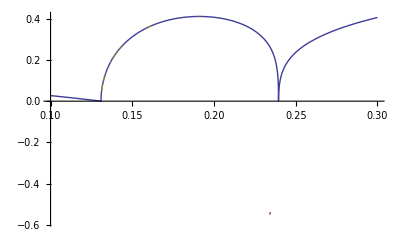

```mathematica
Export["C://1.png", %]
```

Export::noopen: Cannot open "C://1.png".

$Failed

{{1,2},{-1,2}}

$Failed

{{1,2},{-1,2}}

{{1,2},{-1,2}}

```mathematica
S={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
MatrixForm[W={{2*a1,4},{1,3}}]
```

(2 a1 | 4
1 | 3)

(2 a1 | 4
1 | 3)

```mathematica
R=F.W+W.Transpose[F]
```

F.{{2 a1,4},{1,3}}+{{2 a1,4},{1,3}}.Transpose[F]

```mathematica
Solve[{10+4 a1==-1,18-2 a1==0,9-2 a1==0,a1==-1},{w1,w2,w3,w4}]
```

{}

```mathematica
R
```

{{10+4 a1,18-2 a1},{9-2 a1,7}}

General::ivar: {1, 3} is not a valid variable.

Solve[False,{{2 a1,4},{1,3}}]

```mathematica
MatrixForm[R]
```

(10+4 a1 | 18-2 a1
9-2 a1 | 7)

```mathematica
Eigenvalues[R]
```

{1/2 (17+4 a1-√(657-192 a1+32 a1^2)),1/2 (17+4 a1+√(657-192 a1+32 a1^2))}

```mathematica
Eigenvectors[R]
```

{{-(3+4 a1-√(657-192 a1+32 a1^2))/(2 (-9+2 a1)),1},{-(3+4 a1+√(657-192 a1+32 a1^2))/(2 (-9+2 a1)),1}}

```mathematica
Clear[L1Mass]
L1Mass=Array[hg,{3,1200}];
For[ a1=0.601;l=0,a1<1.8,a1=a1+0.001;l++{L1Mass[[1,l]]=a1,L1Mass[[2,l]]=lam1[a1],L1Mass[[3,l]]=lam2[a1]}]
```

```mathematica
Clear[L2Mass]
L2Mass=Array[hg,{2,1801}];
For[ a1=0;l=0,a1<1.8,a1=a1+0.001;l++{L2Mass[[1,l]]=a1,L2Mass[[2,l]]=1/2 (17+4 a1-√(657-192 a1+32 a1^2))}]
```

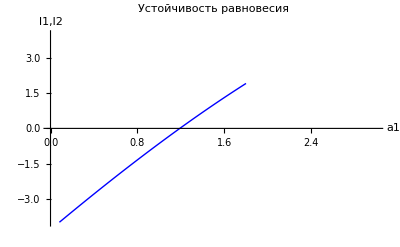

```mathematica
ListPlot[Transpose[L2Mass],PlotStyle->{{Blue,PointSize[Large]}},AxesLabel->{Style["a1",Large],Style["l1,l2",Large]},Joined->True,PlotRange->{{0,3},{-4,4}},PlotLabel->Style[Framed["Устойчивость равновесия"],16]]
```

```mathematica
Export["C:\\Таня\\ПМП\\a1.txt",L2Mass[[1]], "List"]
```

C:\Таня\ПМП\a1.txt

```mathematica
Export["C:\\Таня\\ПМП\\m1.txt",L2Mass[[2]],"List"]
```

C:\Таня\ПМП\m1.txt